```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/zhengyuanyue/Documents/GitHub/Zhengyuan_Lectures_on_Physics/Classical_Mechanics/Rotation/Figures

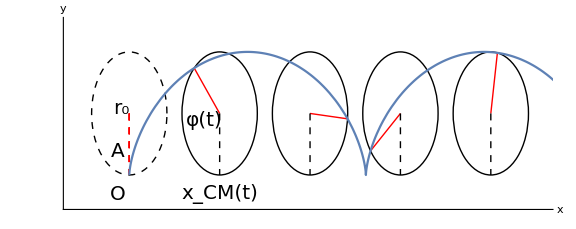

```mathematica
ϕ0=0;ω=1;a=1;b=1;
plate0=Graphics[{Black, Dashed,Circle[{0,a},a]}];
plate[t0_]:=Graphics[{Black, Circle[{ω a t0,a},a]}];
point[t0_]:=Graphics[{Red, Line[{{ω a t0,a},{ω a t0-b Sin[ϕ0+ω t0],a-b Cos[ϕ0+ω t0]}}],Dashed,Line[{{0,a},{-b Sin[ϕ0],a-b Cos[ϕ0]}}]}];
guidelines[t0_]:=Graphics[{Black,Dashed, Line[{{ω a t0,a},{ω a t0,0}}]}];
curve=ParametricPlot[{ω a t-b Sin[ϕ0+ω t],a-b Cos[ϕ0+ω t]},{t,0,11}];
label=Graphics[{Black,Text[Style["A",20],{-0.3,0.4}],Text[Style["O",20],{-0.3,-0.3}],
Text[Style["r_0",Directive[Italic,20]],{-0.2,1.1}],
Text[Style["x_CM(t)",Directive[Italic,20]],{2.4,-0.3}],
Text[Style["φ(t)",20],{2,0.9}]}];
fig=Show[plate0,Table[{plate[t0],point[t0],guidelines[t0]},{t0,2.4,9.6,2.4}],curve,label,Axes->True,AxesLabel->{x,y},Ticks->None,AxesStyle->Directive[20,Black,Thickness[0.002]],PlotRange->{{-1.5,11},{-0.5,2.5}},ImageSize->Large]
```